```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/

```mathematica
(* Thickness *)
th=0.003;
```

## Setup and tests

### Hamiltonians

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with antiperiodic bc *)
ha[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
ha[4,tw,ts]//MatrixForm
```

(0 | 0 | 0 | -tw | 0 | ts | 0 | 0
0 | 0 | 0 | 0 | tw | 0 | ts | 0
0 | 0 | 0 | 0 | 0 | tw | 0 | ts
-tw | 0 | 0 | 0 | 0 | 0 | tw | 0
0 | tw | 0 | 0 | 0 | 0 | 0 | tw
ts | 0 | tw | 0 | 0 | 0 | 0 | 0
0 | ts | 0 | tw | 0 | 0 | 0 | 0
0 | 0 | ts | 0 | tw | 0 | 0 | 0)

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
wf=Block[{val,vec,i=9,ts=10.,tw=1.},
{val,vec}=Eigensystem[hp[i,tw,ts]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

```mathematica
MatrixPlot [Abs[wf],FrameLabel->{"energy label","co-number label"},PlotLabel->"Amplitude labelled by co-number and energy",PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics-

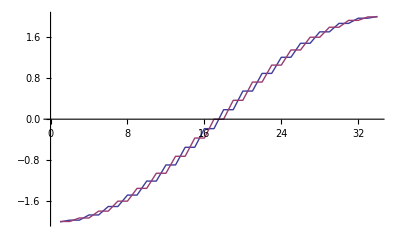

```mathematica
Block[{ts=1.,tw=1.,vpp,vpa,i=7},
vpp=Sort@Eigenvalues[hp[i,tw,ts]];
vpa=Sort@Eigenvalues[ha[i,tw,ts]];
ListPlot[{vpp,vpa},Joined->True,PlotStyle->Thickness[th]]
]
```

```mathematica
Block[{mp,ma,vpp,vpa,i=7},
mp=Table[DiscreteDelta[j-k+1]+DiscreteDelta[j-k+Fibonacci[i+2]-1],{j,Fibonacci[i+2]},{k,Fibonacci[i+2]}];
mp=mp+Transpose@mp;
ma=Table[DiscreteDelta[j-k+1]-DiscreteDelta[j-k+Fibonacci[i+2]-1],{j,Fibonacci[i+2]},{k,Fibonacci[i+2]}];
ma=ma+Transpose@ma;
vpp=Sort[Eigenvalues[mp]//N];
vpa=Sort[Eigenvalues[ma]//N];
ListPlot[{vpp,vpa},Joined->True,PlotStyle->Thickness[th]]
]
```

-Graphics-

### Partition function

```mathematica
(* computation of effective bandwidths *)
Block[{ts=1.,tw=0.99,vpp,vpa,bandlist,dk,invdos,i=15,plot},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
invdos = Table[Cos[k],{k,-Pi/2,Pi/2,Pi/(Fibonacci[i+2]-1)}];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
dk=N[(2Pi)/Fibonacci[i+2]];
plot=ListPlot[{bandlist/dk,invdos},Joined->True,AxesLabel->{"n","dE_n/dk"},PlotLabel->"Inverse DoS \n N = "<>ToString[Fibonacci[i+2]]
,PlotStyle->Thickness[th],PlotLegends->{"Slightly non-periodic system (ρ=0.99)","Period 1 system (ρ=1)"}];
(*Print[plot];*)
Export[dir<>"/data/inverse_dos.pdf",plot];
]
```

les spectres sont calculés !

τ(q=0)=-0.316947

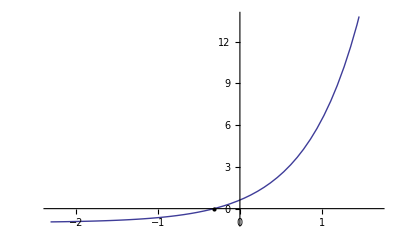

```mathematica
(* fractal dimensions of the spectrum using effective bandwidths as box widths *)
Block[{ts=1.,tw=1./10.,vpp,vpa,vppN,vpaN,bandlist,bandlistN,i=13,gam,gamN,τ0,q0=0},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+1,tw,ts]]];
vpaN=Sort[Eigenvalues[ha[i+1,tw,ts]]];
Print["les spectres sont calculés !"];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
(* calcul des fonctions de partition Subscript[Γ, i] et Subscript[Γ, i+1] *)
gam=Fibonacci[i+2]^-q Plus@@((bandlist)^-τ);
gamN=Fibonacci[i+3]^-q Plus@@((bandlistN)^-τ);
(* Subscript[D, 0] *)
τ0=τ/.FindRoot[(gamN/gam/.q->q0)-1,{τ,-1}];
Print["τ(q=",q0,")=",τ0];
(* vérif que FindRoot ne s'est pas planté *)
Print[Plot[(gamN/gam/.q->q0)-1,{τ,τ0-2,τ0+2},Epilog->{PointSize[Medium],Point[{τ0,0}]}]]
(*ListPlot[{vpp,vpa},Joined->True]*)
]
```